## Examen de Transformada de Funciones 1

#### Problema 1. Determine la transformada de Laplace inversa de la sigiente función

```mathematica
((s+1)*E^(-4s))/(s^3 +2s^2 +5s)
```

(ⅇ^(-4 s) (1+s))/(5 s+2 s^2+s^3)

#### Segundo Teorema de Traslación

```mathematica
Apart[((s + 1)/(s^3 + 2 s^2 + 5 s)),s](*Descomponer en franciones Parciales quitando temporalmente la exponencial*)
```

```mathematica
1/(5 s)+(3-s)/(5 (5+2 s+s^2))(* Factor Comun 1/5 y reincorporamos la exponencial *)
```

1/5 ⅇ^(-4 s) (1/s+(3-s)/(5+2 s+s^2))

```mathematica
1/5 ⅇ^(-4 s) (1/s+(3-s)/((s+1)^2  +4))(*Reescribiendo la ecuacion de manera que se paresca a una ecuación del formulario*)
```

1/5 ⅇ^(-4 s) (1/s+(3-s)/(4+(1+s)^2))

```mathematica
(1/5 )InverseLaplaceTransform[ⅇ^(-4 s) (1/s),s,t]-(1/5 )InverseLaplaceTransform[ⅇ^(-4 s) *((1+s)/(4+(1+s)^2)),s,t]+(2/5)InverseLaplaceTransform[ⅇ^(-4 s) *(2/(4+(1+s)^2)),s,t]//ExpToTrig//FullSimplify
```

### Resultado:

```mathematica
1/10 HeavisideTheta[-4+t] (2-2 ⅇ^(4-t) (Cos[8-2 t]+2 Sin[8-2 t]))(*HeavisideTheta(t-a) es el escalón unitario u(t-a)*)
```

```mathematica
LaplaceTransform[1/10 HeavisideTheta[-4+t] (2-2 ⅇ^(4-t) (Cos[8-2 t]+2 Sin[8-2 t])),t,s]//FullSimplify(*Se comprueba que haciendo Laplace al resultado encontramos la ecuacion original*)
```

(ⅇ^(-4 s) (1+s))/(s (5+s (2+s)))

### Problema 2. Use La Transformada de Laplace para determinar la solucion del siguiente sistema de ecuaciones

```mathematica
(*

x'[t]+x[t]-y'[t]+y[t]==0;
x'[t]+y'[t]+2y[t]==0;
Condiciones:
 y[0]==1;
  x[0]==0;

*)
```

```mathematica
DSolve[{x'[t]+x[t]-y'[t]+y[t]==0,x'[t]+y'[t]+2y[t]==0,y[0]==1,x[0]==0},{y[t],x[t]},t]/.Rule->Equal
```

{{x[t]==-√3 ⅇ^(-t/2) Sin[(√3 t)/2],y[t]==ⅇ^(-t/2) Cos[(√3 t)/2]}}

```mathematica
((1- (s^2 +(5s/2)+1)/(s^2+s+1))/s)//FullSimplify
```

-3/(2 (1+s+s^2))

```mathematica
InverseLaplaceTransform[-3/(2 (1+s+s^2)),s,t]//FullSimplify
```

-√3 ⅇ^(-t/2) Sin[(√3 t)/2]

### Tercer Problema

```mathematica
f[t_]:=A*t/4;(*Este es la funcion Periodica que se repite "n" veces con un periodo de 4*)
T=4;
An=Simplify[(A (2 n π Cos[n π]-Sin[n π]) Sin[n π])/(n^2 π^2),n∈Integers];
Bn=Simplify[(A(-2 n π Cos[2 n π]+Sin[2 n π]))/(2 n^2 π^2),n∈Integers];
A0=Integrate[1/8 A t,{t,0,4}];
Print["A0: ",A0,"\tAn: ",An,"\tBn: ",Bn]
```

A0: A	An: 0	Bn: -A/(n π)

#### Una vez obtenidos los coeficientes se obtiene la siguiente serie de Fourier

```mathematica
A/2 +Sum[-A/(n π)*(Sin[(Pi*n*t)/2]),{n,20}];
Manipulate[Plot[%,{t,-8,8},PlotRange->{-2,13}],{{A,2},1,12}]
```

### Cuarto Problema (1er caso. Ya que se hace mencion de una funcion escaloun unitario y luego se muestra un espectro resultado de la transformada de Fourier que no conincide con el del escalon)

Piecewise[{{1, -3≤t≤3}, {0, True}}]

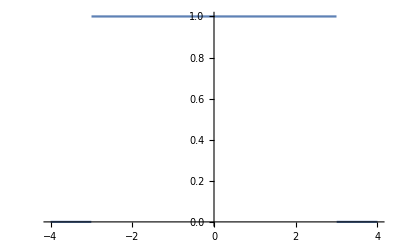

(√(2/π) Sin[3 w])/w

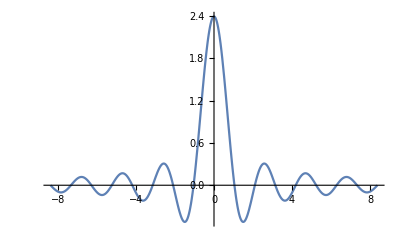

```mathematica
Piecewise[{{1,-3≤t≤3},{0,True}}]
Plot[%,{t,-4,4},PlotRange->All]
f=FourierTransform[%%,t,w]
Plot[f,{w,-8.377580409572781,8.377580409572781},PlotRange->All]
```

#### En Terminos del escalon unitario esta es la función

-HeavisideTheta[-3+t]+HeavisideTheta[3+t]

-Graphics-

(√(2/π) Sin[3 w])/w

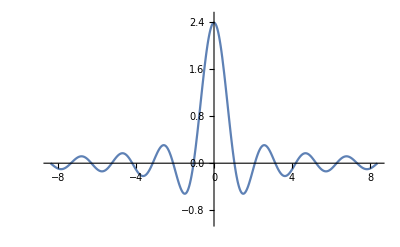

```mathematica
f1=1HeavisideTheta[t-(-3)]+(-1)HeavisideTheta[t-3]
Plot[%,{t,-4,4}]
fT1=FourierTransform[f1,t,w](*Se observa que el resultado es el mismo*)
Plot[fT1,{w,-8.377580409572781,8.377580409572781},PlotRange->{-1,2.5}]
```

#### Vemos que es la misma funcion y la misma transformada, tanto si la expresamos en una funcion por partes como o si la expresamos en terminos del escalon unitario

Cos[4 t] (-HeavisideTheta[-3+t]+HeavisideTheta[3+t])

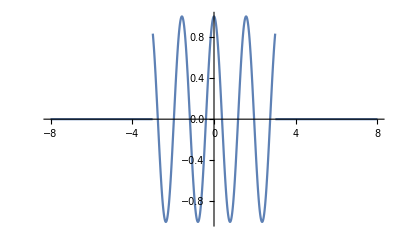

```mathematica
Prod=f1*Cos[4t](*Realizamos el producto que se pide en el problema*)
Plot[%,{t,-8,8},PlotRange->All]
```

```mathematica
FProd=FourierTransform[Prod,t,w](*Esta es la respuesta al producto aplicando transformada de Fourier*)
```

(√(2/π) (-4 Cos[3 w] Sin[12]+w Cos[12] Sin[3 w]))/(-16+w^2)

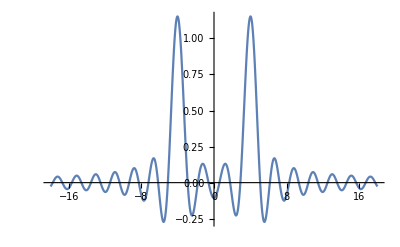

```mathematica
Plot[FProd,{w,-18,18},PlotRange->All]
```

### Cuarto Problema (Caso 2 La grafica que se muestra corresponde a aun funcion Sample de altura 6)

(6 Sin[t])/t

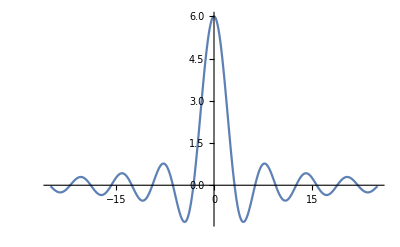

```mathematica
6 Sin[t]/t(*Se declara la funcion Sample de Altura 6 y se observa que la grafica es la misma*)
Plot[(6 (Sin[t]))/t,{t,-25,25},PlotRange->All]
```

-(3 (Sin[3 t]-Sin[5 t]))/t

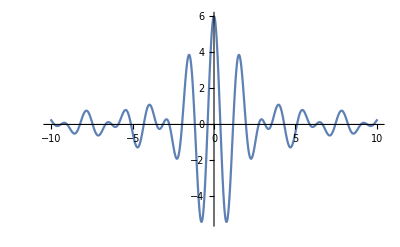

```mathematica
(6 Sin[t]/t)*Cos[4t]//TrigReduce(*Se Realiza el producto que se pide en el problema y se realiza la grafica del producto*)
Plot[%,{t,-10.053096491487338,10.053096491487338},PlotRange->All]
```

-3 ArcTan[3/s]+3 ArcTan[5/s]

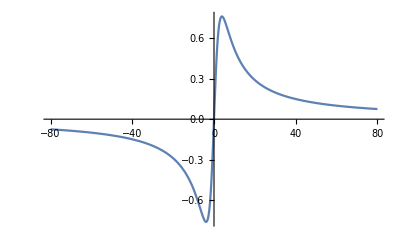

```mathematica
LaplaceTransform[-(3 (Sin[3 t]-Sin[5 t]))/t,t,s]//FullSimplify(*Se realiza la transformada de Laplace del producto y se grafica*)
Plot[%,{s,-80,80},PlotRange->All]
```

### Quinto Problema (Revision)

```mathematica
Fun1=E^(-3t)*HeavisideTheta[t];
Fun2=(1-t)HeavisideTheta[t]+(-(1-t))HeavisideTheta[t-1];
```

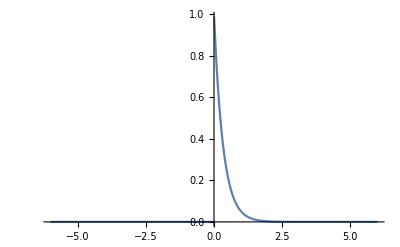

```mathematica
Plot[Fun1,{t,-6.,6.},PlotRange->All]
```

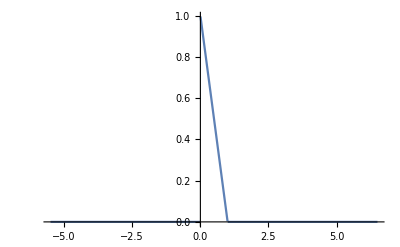

```mathematica
Plot[Fun2,{t,-5.5,6.5}]
```

1/9 ⅇ^(-3 T) (ⅇ^3+ⅇ^(3 T) (-4+3 T)) HeavisideTheta[-1+T]+1/9 (4-4 ⅇ^(-3 T)-3 T) HeavisideTheta[T]

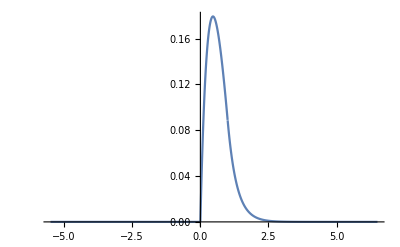

```mathematica
Convolve[Fun1, Fun2, t, T]
Plot[%,{T,-5.5,6.5},PlotRange->All,PlotPoints->2000]
```

```mathematica
Integrate[((1-T)HeavisideTheta[T]+(-(1-T))HeavisideTheta[T-1])*ⅇ^(-3 (t-T)) HeavisideTheta[t-T],{T,0,t}]//FullSimplify
```

ConditionalExpression[1/9 ⅇ^(-3 t) (-4+ⅇ^(3 t) (-4+3 t) (-1+HeavisideTheta[-1+t])+ⅇ^3 HeavisideTheta[-1+t]) HeavisideTheta[t],t∈Reals]

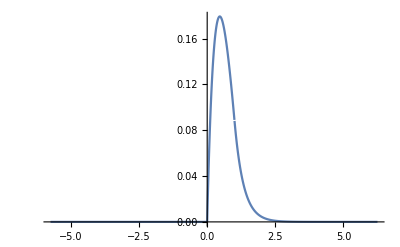

```mathematica
(1/9 ⅇ^(-3 t) (-4+ⅇ^(3 t) (-4+3 t) (-1+HeavisideTheta[-1+t])+ⅇ^3 HeavisideTheta[-1+t]) HeavisideTheta[t]);
Plot[%,{t,-5.75,6.25},PlotRange->All,PlotPoints->2000]
```

ⅇ^(-3 t) HeavisideTheta[t]

(-1+t) HeavisideTheta[-1+t]+(1-t) HeavisideTheta[t]

(ⅇ^-s (1+ⅇ^s (-1+s)))/(s^2 (3+s))

1/9 ⅇ^(-3 t) (-4+ⅇ^(3 t) (4-3 t)+(ⅇ^3+ⅇ^(3 t) (-4+3 t)) HeavisideTheta[-1+t])

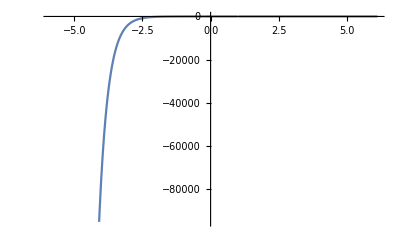

```mathematica
Fun1
Fun2
LaplaceTransform[Fun1,t,s]*LaplaceTransform[Fun2,t,s]//FullSimplify
InverseLaplaceTransform[%,s,t]
Plot[%,{t,-5.875,6.125}]
```